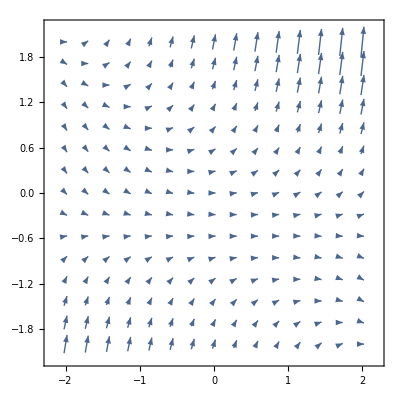

```mathematica
f[x_,t_]:=(x+1/2)*(x+t)
VectorPlot[{1, f[x,t]}, {t,-2,2}, {x,-2,2}]
```

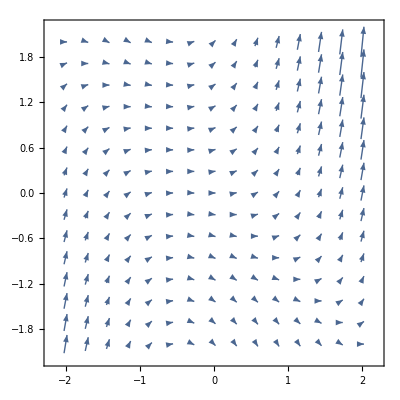

```mathematica
f[x_,t_]:=(x+1/2)*(x+t)
VectorPlot[{1, f[x,t]}, {x,-2,2}, {t,-2,2}]
```

{{y→InterpolatingFunction[{{0., 4.}}, <>]}}

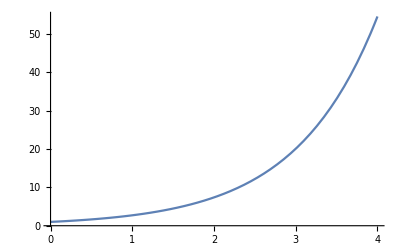

```mathematica
g[y_,t_]:=y
s = NDSolve[{y'[t]==g[y[t],t], y[0]==1}, y, {t,0,4}]
Plot[Evaluate[y[t]/.s], {t,0,4}, PlotRange->All]
```

{{y→InterpolatingFunction[{{-2., 1.}}, <>]}}

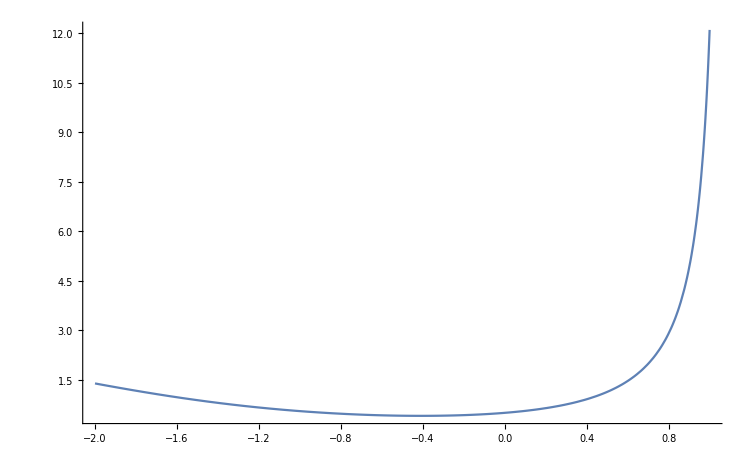

```mathematica
s = NDSolve[{y'[t]==(y[t]+0.5)*(y[t]+t), y[0]==0.5}, y, {t,-2,1}]
Plot[Evaluate[y[t]/.s], {t,-2,1}, PlotRange->All]
```

```mathematica
M=100
s = NDSolve[{y'[t]==y[t]*(1-M/y[t]), y[0]== 110}, y, {t,0,50}]
Plot[Evaluate[y[t]/.s], {t,0,100}, PlotRange->All]
```

100

{{y→InterpolatingFunction[{{0., 50.}}, <>]}}

-Graphics-

100

{{y→InterpolatingFunction[{{0., 50.}}, <>]}}

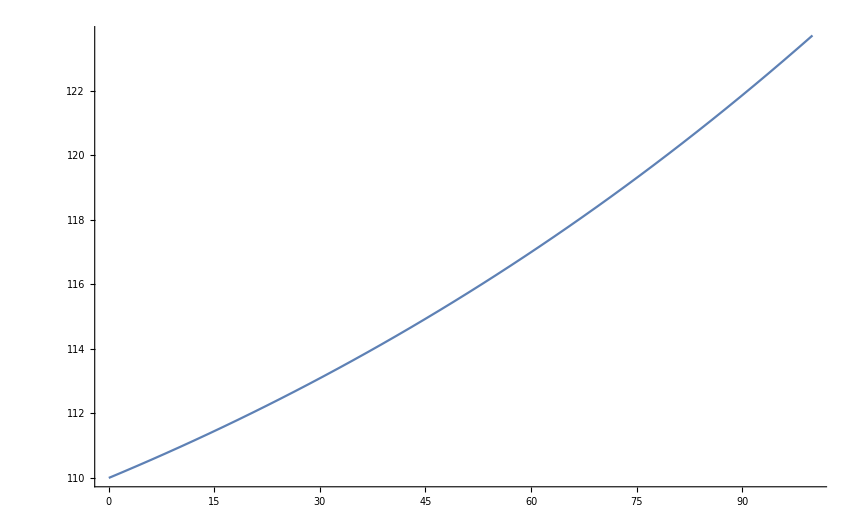

NDSolve::deqn: Equation or list of equations expected instead of (1/2+y[t]) (t+y[t]) in the first argument {(1/2+y[t]) (t+y[t]),y[0]==1/2}.

```mathematica
M=100
s = NDSolve[{y'[t]==(1-M/y[t]), y[0]== 110}, y, {t,0,50}]
Plot[Evaluate[y[t]/.s], {t,0,100}, PlotRange->All]
```

100

{{y→InterpolatingFunction[{{0., 50.}}, <>]}}

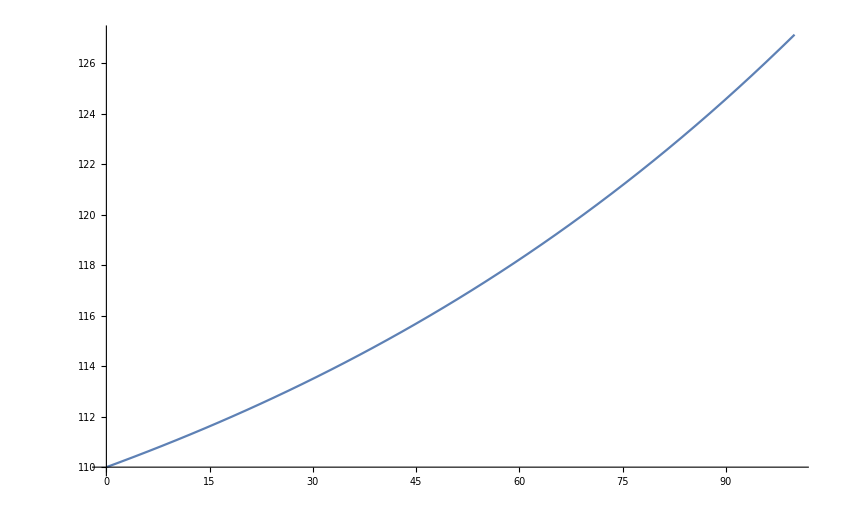

```mathematica
M=100
s = NDSolve[{y'[t]==(y[t]/M- 1), y[0]== 110}, y, {t,0,50}]
Plot[Evaluate[y[t]/.s], {t,0,100}, PlotRange->All]
```

100

{{y→InterpolatingFunction[{{1., 50.}}, <>]}}

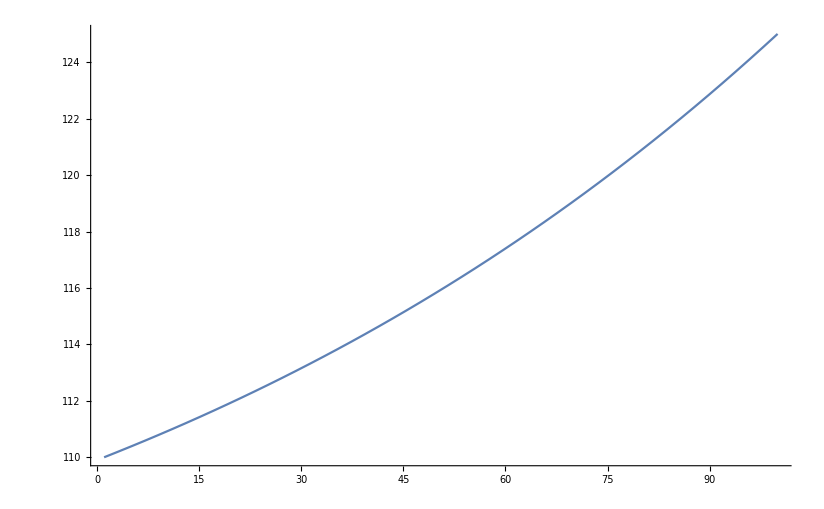

```mathematica
M=100
s = NDSolve[{y'[t]==Log[y[t]/M], y[1]== 110}, y, {t,1,50}]
Plot[Evaluate[y[t]/.s], {t,1,100}, PlotRange->All]
```

100

{{y→InterpolatingFunction[{{1., 50.}}, <>]}}

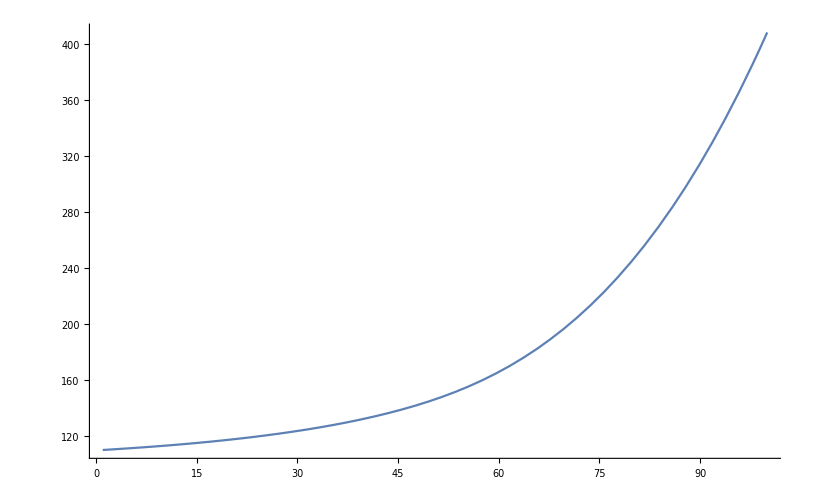

```mathematica
M=100
s = NDSolve[{y'[t]==Exp[y[t]/M]*Log[y[t]/M], y[1]== 110}, y, {t,1,50}]
Plot[Evaluate[y[t]/.s], {t,1,100}, PlotRange->All]
```

100

{{y→InterpolatingFunction[{{0., 50.}}, <>]}}

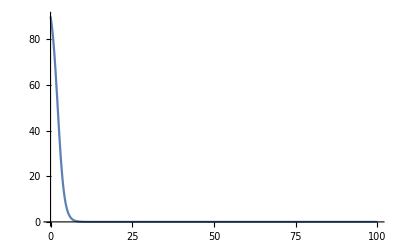

```mathematica
M=100
s = NDSolve[{y'[t]==y[t]*(y[t]/M- 1), y[0]== 90}, y, {t,0,50}]
Plot[Evaluate[y[t]/.s], {t,0,100}, PlotRange->All]
```

```mathematica
M=100
s = NDSolve[{y'[t]==y[t]*(y[t]/M- 1), y[0]== 110}, y, {t,0,50}]
Plot[Evaluate[y[t]/.s], {t,0,100}, PlotRange->All]
```

100

NDSolve::ndsz: At t == 2.39789, step size is effectively zero; singularity or stiff system suspected.

{{y→InterpolatingFunction[{{0., 2.39789}}, <>]}}

-Graphics-

{{y→InterpolatingFunction[{{0., 50.}}, <>]}}

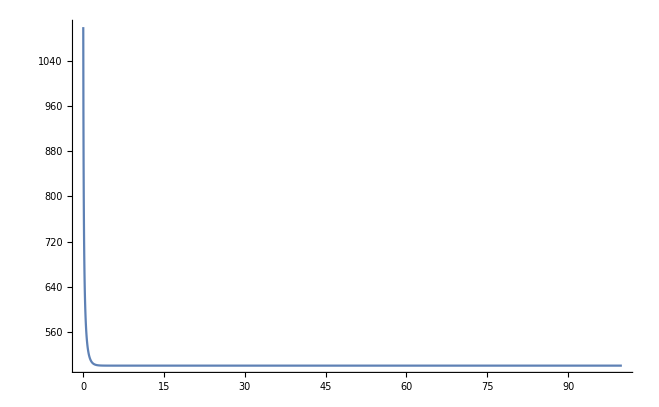

```mathematica
s = NDSolve[{y'[t]==0.5*y[t]*(1-y[t]/500)*(y[t]/100- 1), y[0]== 1100}, y, {t,0,50}]
Plot[Evaluate[y[t]/.s], {t,0,100}, PlotRange->All]
```